```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Elastic Collisions in Lab Frame

```mathematica
Solve[{1/2 m vi^2==1/2 m vf^2+1/2 M v^2,m vi==m vf Cos[θ]+M v Cos[ψ],0==m vf Sin[θ]-M v Sin[ψ]},vf,{ψ,v}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{vf→(2 m vi Cos[θ]-√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))},{vf→(2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))}}

#### Second solution is physical one

```mathematica
Efin=1/2 m((2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M)))^2/.vi->Sqrt[2 ϵ/m];
```

```mathematica
etransfer=FullSimplify[Efin/ϵ,Assumptions->{ϵ>0,M>0,m>0}];
```

```mathematica
1/(2Pi)Integrate[etransfer,{θ,0,2Pi},Assumptions->{ϵ>0,M>0,m>0}]//FullSimplify
```

M^2/(m+M)^2

#### Proper calculation (lab frame angle not exactly isotropic, unlike CM angle) yields ζ= (M^2+m^2)/(m+M)^2~M^2/(m+M)^2for heavy nuclei

```mathematica
ζ=M^2/(m+M)^2;
```

```mathematica
dedxelastic=ϵ(1−ζ) n/Z σ;
```

```mathematica
dedxnonelastic=Piecewise[{{ϵ n/Z σ,ϵ>10},{0,ϵ≤10}}];
```

#### In units of MeV/(10^-5 cm)

```mathematica
Convert[(Mega ElectronVolt)^4 Milli Barn(200 Mega ElectronVolt Fermi)^-2,(Mega ElectronVolt)^2]//N
```

2.5×10^-6 ElectronVolt^2 Mega^2

```mathematica
nucleon=LogLogPlot[ReplaceAll[ReplaceAll[dedxnonelastic,{n->8,Z->6}],{σ->0.1,M->11180,m->1000}](2.5*^-6)(5.*^5),{ϵ,1,10^10},PlotStyle->{Purple,Thick}];
```

```mathematica
meson=LogLogPlot[ReplaceAll[ReplaceAll[dedxnonelastic,{n->8,Z->6}],{σ->0.1,M->11180,m->140}](2.5*^-6)(5.*^5),{ϵ,1,10^10},PlotStyle->{Purple,Thick}];
```

```mathematica
elasticnucleon=LogLogPlot[ReplaceAll[ReplaceAll[dedxelastic,{n->8,Z->6}],{σ->0.1,M->11180,m->1000}](2.5*^-6)(5.*^5),{ϵ,1,10^10},PlotStyle->{Green,Thick}];
```

```mathematica
elasticmeson=elasticnucleon=LogLogPlot[ReplaceAll[ReplaceAll[dedxelastic,{n->8,Z->6}],{σ->0.1,M->11180,m->140}](2.5*^-6)(5.*^5),{ϵ,1,10^10},PlotStyle->{Green,Thick}];
```

```mathematica
canvasnuclear=LogLogPlot[10^20,{ϵ,1,10^10},Frame->True,PlotRange->{10^-3,10^5},FrameLabel->{"MeV","MeV/(10^-5cm)"},PlotLabel->"Stopping Power"];
```

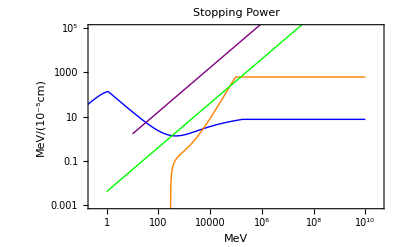

```mathematica
Show[canvasnuclear,proton,protonpauli,elasticnucleon,nucleon]
```

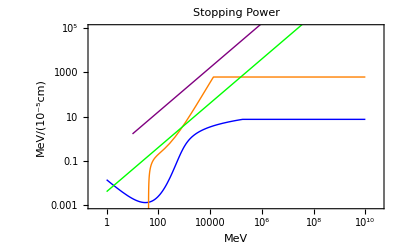

```mathematica
Show[canvasnuclear,pion,pionpauli,elasticmeson,meson]
```

#### Final-state charged hadrons.

```mathematica
finalproton=Convert[NIntegrate[ReplaceAll[dedx^-1,{α->1/137,M->11180,Z->6,n->8,m->1000}],{ϵ,1,10}] 1/(Mega ElectronVolt)*(200 Mega ElectronVolt*Fermi),Centimeter];
```

```mathematica
finalpion=Convert[NIntegrate[ReplaceAll[dedxelastic^-1,{α->1/137,M->11180,Z->6,n->8,m->140,σ->0.1}],{ϵ,1,10}] 1/((Mega ElectronVolt)^3 Milli Barn)*(200 Mega ElectronVolt*Fermi)^3,Centimeter];
```

```mathematica
finalneutron=Convert[NIntegrate[ReplaceAll[dedxelastic^-1,{α->1/137,M->11180,Z->6,n->8,m->1000,σ-> 1}],{ϵ,1,10}] 1/((Mega ElectronVolt)^3 Milli Barn)*(200 Mega ElectronVolt*Fermi)^3,Centimeter];
```

```mathematica
{finalproton,finalpion,finalneutron}//N
```

{3.05095×10^-6 Centimeter,0.00562017 Centimeter,0.0000877382 Centimeter}